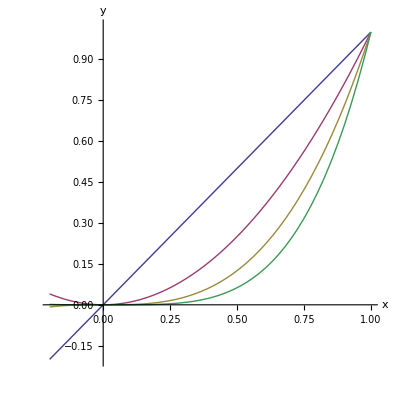

```mathematica
t1=Module[{x,y,n},Plot[Evaluate[Table[x^n,{n,1,4}]],{x,-0.2,1.},AxesLabel->{"x","y"},PlotRange->{-0.2,1.02},AspectRatio->Automatic]]
```

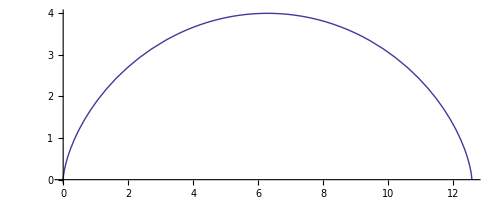

```mathematica
ParametricPlot[{2*(t-Sin[t]),2*(1-Cos[t])},{t,0,2*Pi},AspectRatio->Automatic]
```

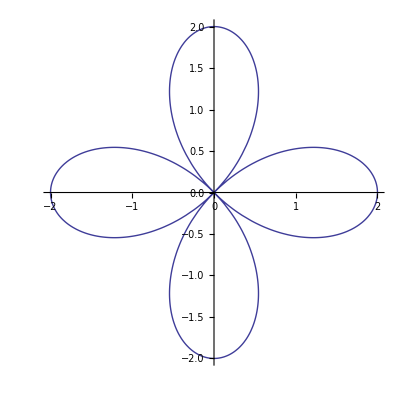

```mathematica
r[t_]:=2*Cos[2*t]
ParametricPlot[{r[t]*Cos[t],r[t]*Sin[t]},{t,0,2*Pi},AspectRatio->Automatic]
```

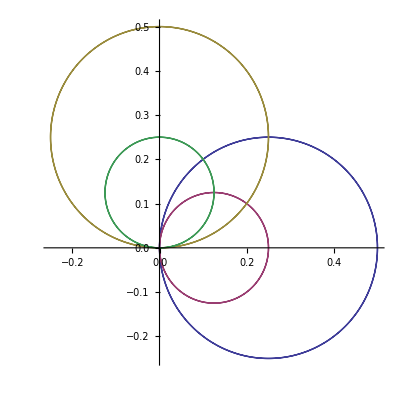

```mathematica
Clear[t]
r[t_]:=0.5*Cos[t];rr[t_]:=0.25*Cos[t];
g[t_]:=0.5*Sin[t];gg[t_]:=0.25*Sin[t];
ParametricPlot[Evaluate[{{r[t]*Cos[t],r[t]*Sin[t]},{rr[t]*Cos[t],rr[t]*Sin[t]},{g[t]*Cos[t],g[t]*Sin[t]},{gg[t]*Cos[t],gg[t]*Sin[t]}}],{t,0,2*Pi},AspectRatio->Automatic]
```

```mathematica
aa={1};ss=N[{3*Sqrt[3]/2},18];n=31;
For[i=2,i≤n,i++,
aa=N[Append[aa,Sqrt[2-2*Sqrt[1-(a[[i-1]]/2)^2]]],18];
ss=N[Append[ss,3*2^(i-2)*a[[i-1]]],18];
]
s1=Table[ss[[i+1]]-ss[[i]],{i,1,n-1}];
Print["n","                      aa","                                 ","ss"]
For[i=1,i≤n-1,i++,
Print[i,"              ",aa[[i]],"               ",ss[[i]]];]
```

n                      aa                                 ss

1              1.               2.59807621135331594

2              0.51763809020504152               3.

3              0.26105238444010318               3.10582854123024915

4              0.13080625846028613               3.1326286132812382

5              0.065438165643552284               3.1393502030468672

6              0.032723463252973563               3.1410319508905096

7              0.016362279207874259               3.1414524722854621

8              0.0081812080524695792               3.1415576079118576

9              0.0040906125823281902               3.1415838921483184

10              0.0020453073606766091               3.1415904632280501

11              0.001022653814027395               3.1415921059992716

12              0.00051132692372483463               3.1415925166921574

13              0.00025566346395130948               3.141592619365384

14              0.00012783173223676626               3.1415926450336909

15              0.000063915866151022071               3.1415926514507677

16              0.000031957933079590903               3.1415926530550368

17              0.000015978966540305435               3.1415926534561041

18              7.9894832702164654×10^-6               3.141592653556371

19              3.9947416351162012×10^-6               3.1415926535814377

20              1.9973708175590967×10^-6               3.1415926535877043

21              9.9868540877967284×10^-7               3.141592653589271

22              4.9934270438985198×10^-7               3.1415926535896627

23              2.4967135219492794×10^-7               3.1415926535897606

24              1.2483567609746421×10^-7               3.1415926535897851

25              6.2417838048732136×10^-8               3.1415926535897912

26              3.1208919024366072×10^-8               3.1415926535897927

27              1.5604459512183036×10^-8               3.1415926535897931

28              7.8022297560915183×10^-9               3.1415926535897932

29              3.9011148780457591×10^-9               3.1415926535897932

30              1.9505574390228796×10^-9               3.1415926535897932

(_(n → ∞)^Limitxn=)1/2

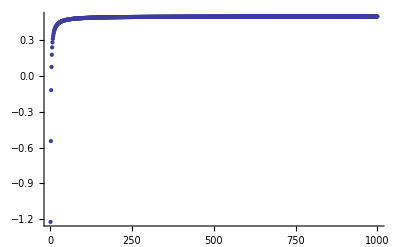

```mathematica
n=.;
x=Table[(n^3-3*n^2+n-10)/(2*n^3-n+8),{n,1,1000}]//N;
x0=Limit[(n^3-3*n^2+n-10)/(2*n^3-n+8),n->Infinity];
Print["(_(n → ∞)^Limitxn=)",x0]
ListPlot[x]
```

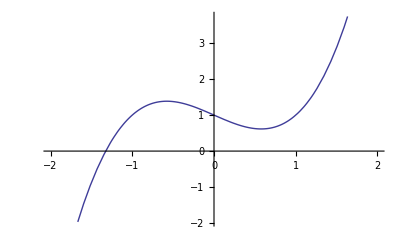

-1+3 z^2

6 z

```mathematica
f[z_]:=z^3-z+1;
Plot[z^3-z+1,{z,-2,2}]
D[f[z],z]
D[f[z],{z,2}]
```

```mathematica
f[x_]:=x^3-x+1;
x0=-2.;delta=10^(-4);imax=10;
For[i=1,i≤imax,i++,
x1=x0-f[x0]/f'[x0];
Print[x1];
If[Abs[x1-x0]>delta,x0=x1,Break[]];
]
```

-1.54545

-1.35961

-1.3258

-1.32472

-1.32472

```mathematica
FindRoot[z^3-z+1,{z,-2}]
```

{z→-1.32472}

```mathematica
Integrate[z^2,{z,0,1}]//N
```

0.333333

```mathematica
f[x_]:=x^2;
n=Input["n="];
s=0;a=0;b=1;
h=(b-a)/n;
For[i=1,i≤n-1,i++,
s=s+f[a+h*i]*h;]
s//N
```

0.333328

```mathematica
a=126.6324;
f1[y_]=a*Cosh[y/a];
f[y_]:=Sqrt[1+f1'[y]^2];
n=Input["n="];
s=0.;a=-50.;b=50.;h=(b-a)/n;
For[i=1,i<n-1,i++,
s=s+f[a+i*h];
]
s1=NIntegrate[f[y],{y,-50,50}]
s=(s+(f[a]+f[b])/2)*h
```

102.619

102.511

```mathematica
DSolve[{y'[x]==E^x*y[x],y[0]==E},y[x],x]
```

{{y[x]→ⅇ^(ⅇ^x)}}

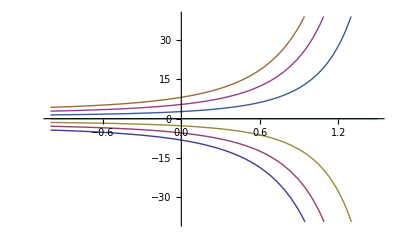

```mathematica
t=Table[c*ⅇ^(ⅇ^x) ,{c,-3,3}];
Plot[Evaluate[t],{x,-1,1.5}]
```

```mathematica
DSolve[{x*y'[x]+2*y[x]==E^x},y[x],x]
```

```mathematica
{{y[x]->(ⅇ^x (-1+x))/x^2+C[1]/x^2}}
```

{{y[x]→(ⅇ^x (-1+x))/x^2+C[1]/x^2}}

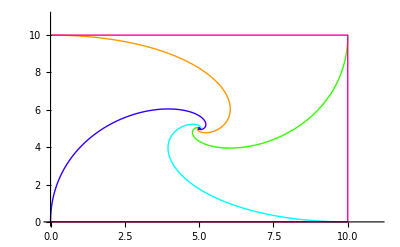

```mathematica
t=12;dt=0.02;v=1;n=t/dt;a=10;
robit={{{0,a}},{{a,a}},{{a,0}},{{0,0}}};
For[j=1,j≤n,j++,
For[i=1,i≤4,i++,xx1=robit[[i,j,1]];yy1=robit[[i,j,2]];
If[i≠4,xx2=robit[[i+1,j,1]];yy2=robit[[i+1,j,2]],
xx2=robit[[1,j,1]];yy2=robit[[1,j,2]]];
dd=Sqrt[(xx2-xx1)^2+(yy2-yy1)^2]//N;
xx1=xx1+v*dt*(xx2-xx1)/dd;
yy1=yy1+v*dt*(yy2-yy1)/dd;
robit[[i]]=Append[robit[[i]],{xx1,yy1}]]];
g1=ListPlot[robit[[1]],PlotJoined->True,
PlotRange->{{0,a},{0,a}},PlotStyle->{Hue[0.1],PointSize[1]}];
g2=ListPlot[robit[[2]],PlotJoined->True,PlotRange->{{0,a},{0,a}},PlotStyle->{Hue[0.3],PointSize[1]}];
g3=ListPlot[robit[[3]],PlotJoined->True,PlotRange->{{0,a},{0,a}},PlotStyle->{Hue[0.5],PointSize[1]}];
g4=ListPlot[robit[[4]],PlotJoined->True,PlotRange->{{0,a},{0,a}},PlotStyle->{Hue[0.7],PointSize[1]}];
g5=ListPlot[{{0,a},{a,a},{a,0},{0,0}},PlotJoined->True,PlotRange->{{0,a},{0,a}},PlotStyle->{Hue[0.9],PointSize[1]}];
Show[{g1,g2,g3,g4,g5},PlotRange->{{0,a+1},{0,a+1}}]
```

```mathematica
f[x_,y_]:=x*y/(x^2+y^2)
Plot3D[f[x,y],{x,-1,1},{y,-1,1},PlotPoints->50]
```

-Graphics3D-

```mathematica
tu=ParametricPlot3D[{Cos[u]*Sin[v],Sin[u]*Sin[v],Cos[v]},{u,0,2*Pi},{v,0,Pi},PlotPoints->50,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Clear [x,y,z1,z2]
z1=3-x^2-y^2;
z2=x^2+y^2;
x=r*Cos[u];y=r*Sin[u];
t=ParametricPlot3D[{{x,y,z1},{x,y,z2}},{u,0,2*Pi},{r,0,1},AspectRatio->Automatic,ViewPoint->Top]
ParametricPlot3D[{{x,y,z1},{x,y,z2}},{u,0,2*Pi},{r,0,1},AspectRatio->Automatic,ViewPoint->Front]
ParametricPlot3D[{{x,y,z1},{x,y,z2}},{u,0,2*Pi},{r,0,1},AspectRatio->Automatic,ViewPoint->{Pi,Pi/2,0}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Clear[x]
Series[Cos[x],{x,0,4}]
Normal[Series[E^x,{x,0,5}]]
```

1-x^2/2+x^4/24+O[x]^5

1+x+x^2/2+x^3/6+x^4/24+x^5/120

```mathematica
(*您的成绩总分：518*
听力：174
阅读：189
综合：52
写作：103*)
```

```mathematica
(*听力249分，阅读249分，完型填空或改错70分，作文142分*)
249*2+70+142
```

710

```mathematica
(*{"☹","☺"}*happtsmile)
```

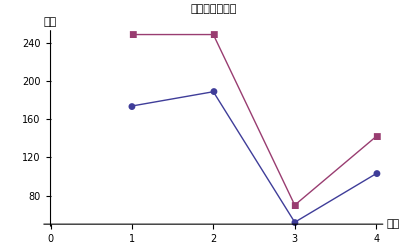

```mathematica
ListLinePlot[{{174,189,52,103},{249,249,70,142}},PlotLegend->{"我的成绩","标准成绩"},LegendPosition->{1,0},PlotMarkers->Automatic,AxesLabel->{"板块","成绩"},PlotLabel->"四级成绩分析图"]
```

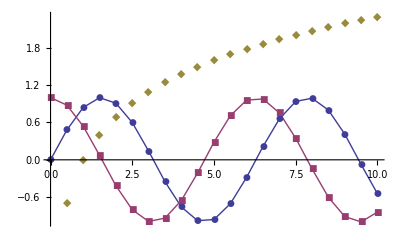

```mathematica
ListPlot[Table[{x,f[x]},{f,{Sin,Cos,Log}},{x,0,10,0.5}],PlotLegend->{"Sine","Cosine","Log"},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic]
```

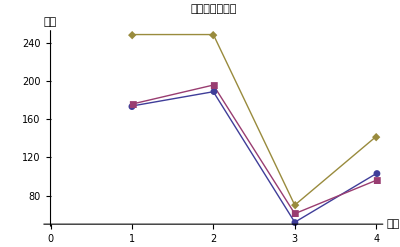

```mathematica
ListLinePlot[{{174,189,52,103},{176,196,61,96},{249,249,70,142}},PlotLegend->{"师争明","韩速","标准成绩"},LegendPosition->{1,0},PlotMarkers->Automatic,AxesLabel->{"板块","成绩"},PlotLabel->"四级成绩分析图"]
```

```mathematica
B=Array[b,{3,3}];
MatrixForm[%]
```

(b[1,1] | b[1,2] | b[1,3]
b[2,1] | b[2,2] | b[2,3]
b[3,1] | b[3,2] | b[3,3])

```mathematica
B={{1,2,3},{4 ,5,6},{7,8,0}};
Inverse[B];
Det[B]
Inverse[B];
MatrixForm[%]
```

27

(-16/9 | 8/9 | -1/9
14/9 | -7/9 | 2/9
-1/9 | 2/9 | -1/9)

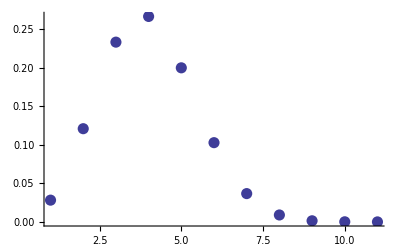

```mathematica
bdist=BinomialDistribution[10,0.3];t1=Table[PDF[bdist,i],{i,0,10}];
ListPlot[t1,PlotStyle->PointSize[0.02]]
```

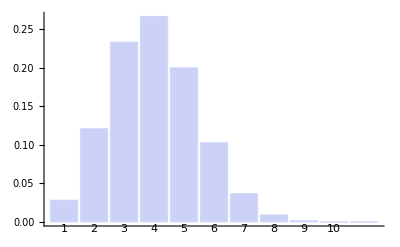

```mathematica
BarChart[t1,ChartLabels->{Table[i,{i,1,10}]}]
```

```mathematica
ndist=NormalDistribution[0,1];
pdf=PDF[ndist,x]
```

NormalDistribution[0,1]

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
f[a_] :=Module[{x = 1.,xp},
Label[begin];
If[Abs[xp - x] < 10^-8,Goto[end]];
xp = x;
x = (x+a/x)/2;
Goto[begin];
Label[end];
x]
```

```mathematica
f[3]
```

1.73205

```mathematica
(*下面的程序有问题，结果应该为0.69*)
t=0;m=0;n=0;
Label[begin];
y=0;x=Table[Random[Integer,{1,365}],{30}];
For[i=1,i≤29,i++,
For[j=i+1,j≤30,j++,
If[x[[j]]==x[[i]],y=1,Break[]];]]
n=n+y;m=m+1;
If[m≤100,Goto[begin];]
h=n
Print[N[n/(m-1)]]
```

```mathematica
rool:={Random[Integer,{1,6}],RandomInteger[{1,6}]};
A=Table[rool,{100}];
b=Table[0,{100}];For[i=1,i≤100,i++,
b[[i]]=A[[i,1]]+A[[i,2]];]
b
```

{7,4,7,11,7,9,12,9,10,7,5,5,12,6,2,9,8,9,7,10,4,4,5,6,4,5,9,7,4,9,5,8,7,4,10,10,9,6,5,10,5,9,5,7,5,9,7,6,9,6,5,10,5,6,7,10,6,11,3,10,7,7,3,8,5,7,9,6,7,9,8,7,10,2,8,7,9,10,6,9,5,8,8,6,6,9,6,7,2,6,8,12,8,4,6,7,7,7,7,7}

{0,3,2,7,13,14,22,9,15,10,2}

{0.,0.03,0.02,0.07,0.13,0.14,0.22,0.09,0.15,0.1,0.02}

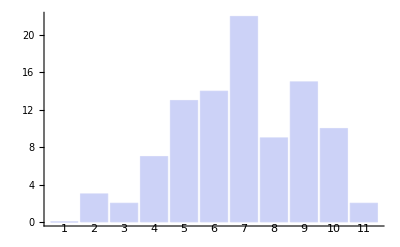

```mathematica
(*分组统计频数和计算频率*)
bo1=BinCounts[b,{1,12,1}]
bo2=bo1/100//N
BarChart[bo1,ChartLabels->{Table[i,{i,1,12}]}]
```

```mathematica
n=Input["试验总次数n="];
x=Table[Random[Integer],{n}];
na=0;
For[i=1,i<n,i++,
If[x[[i]]==0,na=na+1]
]
n
na
na/n//N
```

24000

11823

0.492625

```mathematica
n=Input["n="]
k=0;
For[i=1,i<n,i++,x=Random[Real,{0,Pi}];
y=Random[Real,{0,Pi}];
If[y<Sin[x],k=k+1]]
pi=Sqrt[2*n/k];
Print["π=",N[pi,18]]
```

50000

π=3.15079815888330686

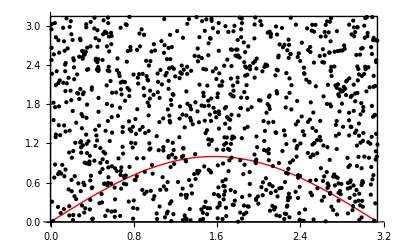

```mathematica
p1=Graphics[Plot[Sin[x],{x,0,Pi},PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity]];
p2=Graphics[Line[{{0,Pi},{Pi,Pi},{Pi,0},{0,0},{0,Pi}}]];
p=Graphics[Table[Point[{Random[Real,{0,Pi}],Random[Real,{0,Pi}]}],{i,1,1000}]];
Show[p1,p2,p,PlotRange->{0,Pi}]
```

```mathematica
n=Input["n="];
k=0;
For[i=1,i<n,i++,
x=Random[Real,{-1,1}];y=Random[Real,{-1,1}];
If[x^2+y^2≤1,k=k+1;]
]
Print["π=",N[4*k/n,10]]
```

π=3.1464

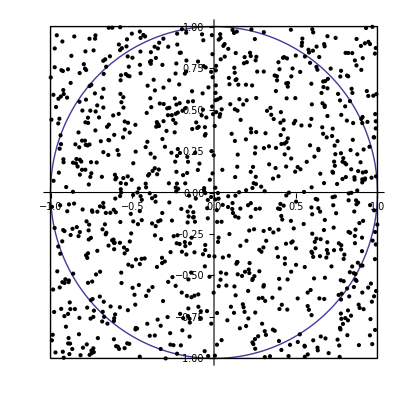

```mathematica
p=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi}];
p1=Graphics[Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]];
p2=Graphics[Table[Point[{Random[Real,{-1,1}],Random[Real,{-1,1}]}],{i,1,1000}]];
Show[p,p1,p2]
```

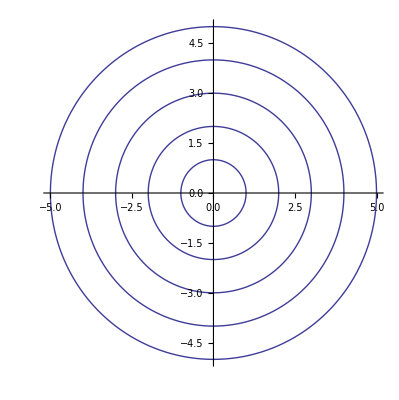

```mathematica
myplot[r_]:=ParametricPlot[{r*Cos[t],r*Sin[t]},{t,0,2*Pi},AspectRatio->Automatic]
Map[myplot,{1,2,3,4,5}];
Show[%,PlotRange->{-5,5}]
```

```mathematica
x={Sqrt[2]//N};
For[i=2,i≤10,i++,
x=Append[x,Sqrt[2+x[[i-1]]]];
]
x
```

{1.41421,1.84776,1.96157,1.99037,1.99759,1.9994,1.99985,1.99996,1.99999,2.}

```mathematica
(*求解平面三点的面积*)
s[x_List,y_List,z_List]:=Module[{a,b,c},a=Prepend[x,1];b=Prepend[y,1];c=Prepend[z,1];
Abs[Det[{a,b,c}]/2]];
s[{1,2},{0.4,5},{3,7.6}]
```

4.68

```mathematica
(*求解拉格朗日中值定理的c f'[c]=(f[b]-f[a])/b-a*)
Lagrange[f_,a_,b_]:=Module[{v,u,t,c,s,q,w={ }},v=Variables[f][[1]];
u=D[f,v];t=((f/.v->b)-(f/.v->a))/(b-a);
s=Solve[u==t,v];
For[i=1,i<=Length[s],i++,
If[N[(v/.s[[i]])]>a&&N[(v/.s[[i]])]<b,
w=Append[w,v/.s[[i]]]
];
];
w];
Lagrange[t+ArcTan[t],0,1]//N
```

{0.522723}

```mathematica
Lagrange[x^2+3*x+2,1,8]//N
```

{4.5}